# Graph Theory

## First definition and example

Definition of a graph: A graph is a pair (V,E), where V is a finite set (called the vertices) and E is a subset of the size-2 subsets of V (called the edges).

We picture the vertices as dots and the edges as lines.

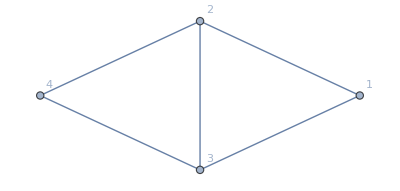

```mathematica
G=Graph[{1<->2,2<->3,3<->1,4<->3,4<->2},VertexLabels->"Name"]
```

### Graph definitions

- We call two vertices  adjacent if . We write this as  . In the example graph G, the vertices 2 and 3 are adjacent, but 4 and 1 are not. We sometimes add a subscript   to clarify that v is adjacent to w in the graph G.
- The set of vertices adjacent to  is the neighborhood of , written as . We call these vertices  the neighbors of v. In the example graph, .
- We call two vertices  connected if we can reach v from w through a series of adjacencies. In the example graph, all pairs of vertices are connected.
- We call the graph G connected if every pair of vertices of G are connected. The example graph G is connected.
- If  and   for some , then we say that  is incident to . We also say that  is incident to .
- The number of edges incident to a vertex  is called the degree . In the example graph, .
-The degree of a graph is the largest degree of a vertex, written . For the example graph, .
-A graph is called regular if every vertex has the same degree. The example graph is not regular.

### Rules of graphs and the variants produced by breaking them

The standard definition of a graph places some restrictions on its structure. We list some of these restrictions and give the word for the object that results from removing them.

Since  consists of size size-2 subsets of V, no vertex is adjacent to itself. . If we decide to break this rule, then we get a graph with loops.
There is at most one edge between any two vertices. If we decide to break this rule, then we get a multigraph.
The edges are a symmetric relationship on the vertices. If v is adjacent to w, then w is adjacent to v. If we decide to break this rule, then we get a directed graph (digraph).
The edges are relationships between pairs of vertices. If we decide to break this rule, then we get a hypergraph.
The graph itself does not know about the locations of its vertices. The drawing of a graph is a representation that includes extra information, unrelated to the graph itself. If we decide to break this rule, then we get an embedded graph.
We assume that the set V is finite. It is coherent to discuss infinite graphs, where .

We sometimes use the words simple graph to emphasize that the object really is a graph, and not a variant such as a multigraph.

Even though we usually think of graphs in terms of diagrams like the one above, the true mathematical graph is just an abstract configuration of adjacencies. The same graph can be drawn in different ways.
Here is another drawing of our example graph, G.

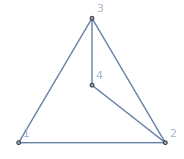

```mathematica
Graph[{1<->2,2<->3,3<->1,4<->3,4<->2},VertexLabels->"Name",VertexCoordinates->{{0,0},(*vertex 1*){1/2,0},(*vertex 2*){0.5/2,0.866/2},(*vertex 3*){0.5/2,0.4/2}    (*vertex 4 inside the triangle*)}]
```

### Isomorphism Classes

Technically speaking, the vertices of a graph are labeled. Technically, our example graph G is different from what would result if we swapped the label of vertex 4 and vertex 3. In G, vertex 4 is not adjacent to 1, but it would be if we swapped the labels.
Usually, we don’t care about the labels, and want to focus on the structure of the graph, as drawn below:

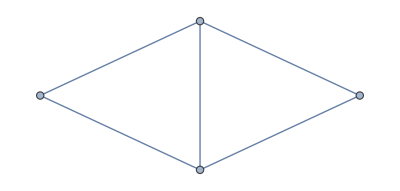

```mathematica
Graph[{1<->2,2<->3,3<->1,4<->3,4<->2}]
```

These unlabeled graphs are called isomorphism classes of graphs. It is common to use the term “graph” to really refer to “isomorphism class of graphs.” This can cause confusion, so beware. Depending on the context, you may need to clarify whether you mean graphs or isomorphism classes.

### Representing Graphs

In addition to drawing the graph using points for vertices and lines for edges, we can explicitly write down the adjacencies in any of 3 ways.

#### Adjacency List

An adjacency list provides a list of neighbors of each vertex. Here is the adjacency list for our graph G.

```mathematica
AssociationThread[VertexList[G],AdjacencyList[G]]
```

<|1→{2,3},2→{1,3,4},3→{1,2,4},4→{2,3}|>

#### Adjacency Matrix

An adjacency matrix is a  grid, where the rows and columns are indexed by . We write 1 in a cell when the corresponding vertices for that cell’s row and column are adjacent, and 0 otherwise.

```mathematica
vertices=VertexList[G];
Grid[Prepend[MapThread[Prepend,{Normal[AdjacencyMatrix[G]],vertices}],Prepend[vertices,""]],Frame->All]
```

| 1 | 2 | 3 | 4
1 | 0 | 1 | 1 | 0
2 | 1 | 0 | 1 | 1
3 | 1 | 1 | 0 | 1
4 | 0 | 1 | 1 | 0

This matrix depends on an assumed ordering of the vertices . If the vertices are listed in a different order, you will get a different adjacency matrix.
Notice that the adjacency matrix always has 0’s on the diagonal.

#### Edge List

An edge list is a list of all of the edges that appear in the graph. It is the default way to create a graph in Mathematica and some other computer systems.

```mathematica
EdgeList[G]
```

{1<->2,2<->3,3<->1,4<->3,4<->2}

## Applications of Graphs

Graphs are very general and can be applied in a variety of situations. Here are some ways to think about the vertices and edges of a graph.
- A social network (vertices are people, edges are friendships.)
- A computer network (vertices are computer, edges are connections.)
- Molecular graphs (vertices are atoms, edges are bonds.)
- Constraint/contradiction graph (vertices are propositions. Edges are when the propositions cannot be simultaneously satisfied.)
- Location graph (vertices are physical objects, edges are when the objects are close.)
- Transportation graph (vertices are locations. Edges are when there is transportation between the edges.)
- Transition graphs (vertices are states of an object. There is an edge between two states if it’s possible to move from one state to the other.)
- Hasse diagrams (vertices are objects. There is an edge if one object contains another.)

## Basic examples

Let’s describe some basic examples of graphs.

### Edge Cases: The empty graph, the singleton graph

It may happen that  in a graph. This is the empty graph, with no vertices and no edges.
If , then there is only one graph on that vertex set. There are no edges.

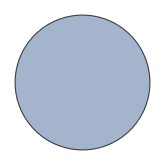

```mathematica
Graph[{1},{}]
```

### Path Graphs

Let . The path graph on  vertices has , and .
For example, when , we have the following path graph.

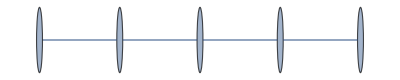

```mathematica
PathGraph[Range[5]]
```

Notice that in the graph P(n), there are n-1 edges. The length of the path is the number of edges, n-1.

### Cycle Graphs

If we start with a path on n vertices and add another edge between the first and nth vertices, then we obtain a cycle graph.

The cycle graphs have as many edges as vertices.

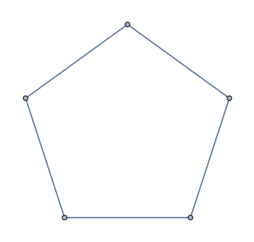

```mathematica
CycleGraph[5]
```

### Star Graphs

The star graph on n vertices has one central vertex that is adjacent to all of the other vertices.

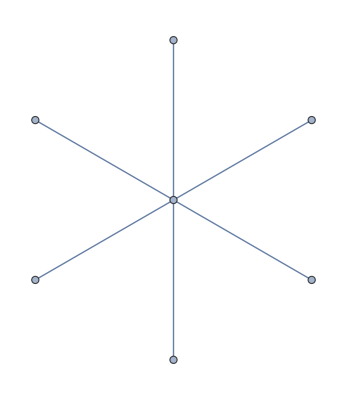

```mathematica
StarGraph[7]
```

### Complete Graphs

The complete graph on n vertices, written , is the graph where each vertex is adjacent to each other vertex.



```mathematica
CompleteGraph[5]
```

### Complete Bipartite Graphs

If we split the vertices into two groups, so that each vertex in one group is adjacent to each vertex in the other group, then we get a complete bipartite graph. Note that this generalizes the star graph.

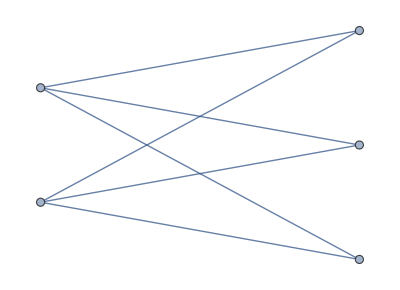

```mathematica
CompleteGraph[{2,3}]
```

### Cube Graph

Let  and let  be the set of length-n bitstrings. Declare two vertices to be adjacent if they differ in exactly one coordinate. For example, when n=3, 001 is adjacent to 101.The result is the cube graph, or hypercube graph.

These graphs are important because their vertices can be thought of as digital information, and their edges model bit-flipping errors.

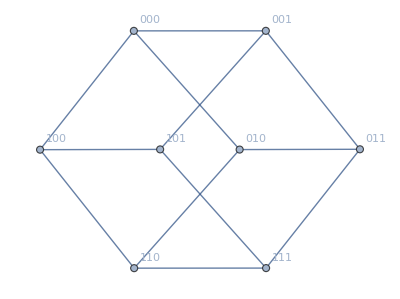

```mathematica
g=HypercubeGraph[3];
vertices=VertexList[g];

HypercubeGraph[3,VertexLabels->(Thread[vertices->IntegerString[vertices-1,2,3]])]
```

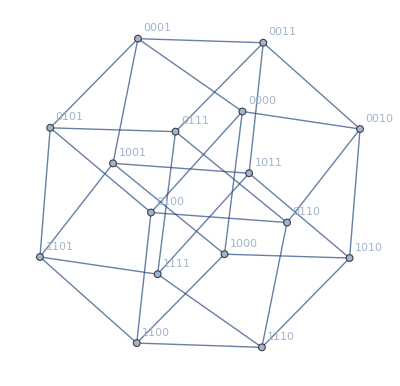

```mathematica
g=HypercubeGraph[4];
vertices=VertexList[g];

HypercubeGraph[4,VertexLabels->(Thread[vertices->IntegerString[vertices-1,2,4]])]
```

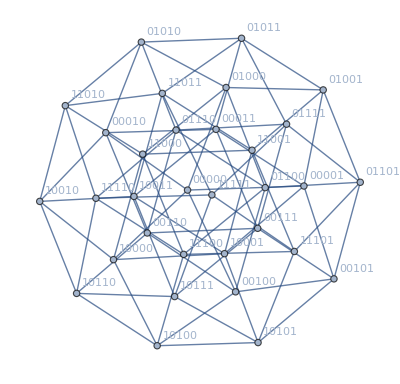

```mathematica
g=HypercubeGraph[5];
vertices=VertexList[g];

HypercubeGraph[5,VertexLabels->(Thread[vertices->IntegerString[vertices-1,2,5]])]
```

## Operations on Graphs

We’ve seen a few examples of simple graphs. Now we discuss how to build new graphs.
For reference, here is our graph .

```mathematica
G
```

-Graphics-

### Complement

If  is a graph, then its complement  is the graph , where we abuse notation and write  for the set of size-2 subsets of . In other words,  has the same vertex set as , and the edges of  are the non-edges of . Note that  is still a simple graph, since vertices of  are not adjacent to themselves.

Here is the complement of , .

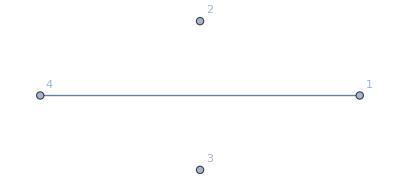

```mathematica
GraphComplement[G]
```

### Line Graph

If  is a graph, then its line graph is the graph , where  is the set of pairs of distinct edges that share a vertex.

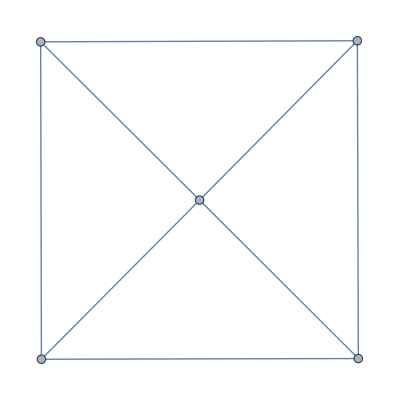

```mathematica
LineGraph[G]
```

### Disjoint Union

Let  and  be graphs. We assume . The disjoint union  is the graph whose vertex set is , and whose edge set is  if  or if .

The disjoint union simply places the two graphs  and  into the same graph, without introducing connections between the two graphs. This provides examples of graphs that are not connected.

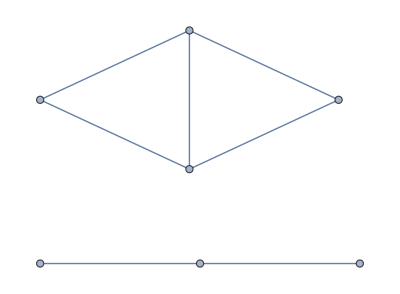

```mathematica
GraphDisjointUnion[G,PathGraph[Range[3]]]
```

### Products

There are several different products on graphs. For each of these products, the vertex set is the Cartesian products of the vertex sets of the input graphs. The edge sets differ slightly. Here is a summary, copied from the documentation and formatted with AI.

```mathematica
Grid[{ {"Type of product", "Condition for (u1,u2)~(v1,v2)"},{"Cartesian","(u1 == v1 ∧ u2 ⟷ v2) ∨ (u2 == v2 ∧ u1 ⟷ v1)"},{"Conormal","(u1 ⟷ v1) ∨ (u2 ⟷ v2)"},{"Lexicographical","(u1 ⟷ v1) ∨ (u1 == v1 ∧ u2 ⟷ v2)"},{"Normal","(u1 == v1 ∧ u2 ⟷ v2) ∨ (u2 == v2 ∧ u1 ⟷ v1) ∨ (u1 ⟷ v1 ∧ u2 ⟷ v2)"},{"Rooted","(u1 == v1 ∧ u2 ⟷ v2) ∨ (u1 ⟷ v1 ∧ u2 == v2 == r)"},{"Tensor","(u1 ⟷ v1) ∧ (u2 ⟷ v2)"}},Frame->All,Background->{None,{LightGray,{White}}},Alignment->Left,Spacings->{2,1},ItemStyle->Directive[FontFamily->"Courier",FontSize->14]]
```

Type of product | Condition for (u1,u2)~(v1,v2)
Cartesian | (u1 == v1 ∧ u2 ⟷ v2) ∨ (u2 == v2 ∧ u1 ⟷ v1)
Conormal | (u1 ⟷ v1) ∨ (u2 ⟷ v2)
Lexicographical | (u1 ⟷ v1) ∨ (u1 == v1 ∧ u2 ⟷ v2)
Normal | (u1 == v1 ∧ u2 ⟷ v2) ∨ (u2 == v2 ∧ u1 ⟷ v1) ∨ (u1 ⟷ v1 ∧ u2 ⟷ v2)
Rooted | (u1 == v1 ∧ u2 ⟷ v2) ∨ (u1 ⟷ v1 ∧ u2 == v2 == r)
Tensor | (u1 ⟷ v1) ∧ (u2 ⟷ v2)

We will draw the Cartesian, Conormal, Normal, and Tensor products. They are more natural than the others, because they treat both graphs equally.

#### Cartesian Product.

The edges of the Cartesian product are between two pairs of vertices, so that the pairs match in one coordinate and are adjacent in the other.

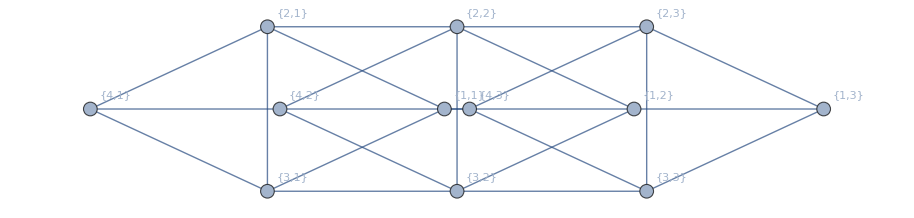

```mathematica
GraphProduct[G,PathGraph[Range[3]],"Cartesian",VertexLabels->"Name"]
```

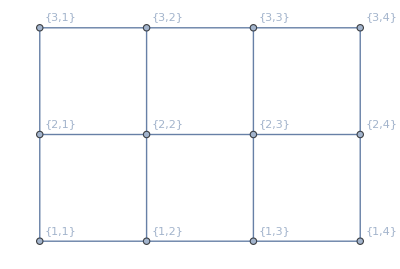

```mathematica
GraphProduct[PathGraph[Range[3]],PathGraph[Range[4]],"Cartesian",VertexLabels->"Name",GraphLayout->"GridEmbedding"]
```

#### Conormal Product

The conormal product has an edge between two pairs of vertices if there is an edge between the vertices in a coordinate. In this construction, we rely on the fact that vertices are never adjacent to themselves in simple graphs.

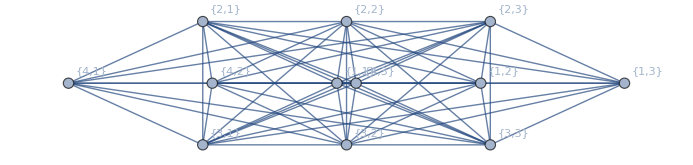

```mathematica
GraphProduct[G,PathGraph[Range[3]],"Conormal",VertexLabels->"Name"]
```

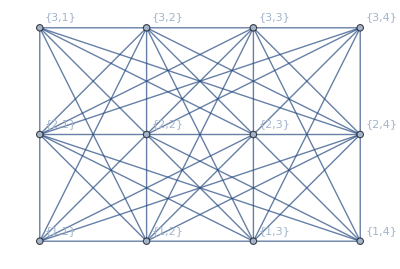

```mathematica
GraphProduct[PathGraph[Range[3]],PathGraph[Range[4]],"Conormal",VertexLabels->"Name",GraphLayout->"GridEmbedding"]
```

#### Normal

The normal product has an edge between two pairs of vertices if both coordinates are adjacent or equal.

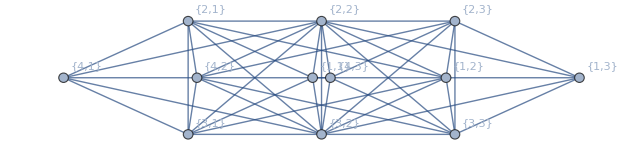

```mathematica
GraphProduct[G,PathGraph[Range[3]],"Normal",VertexLabels->"Name"]
```

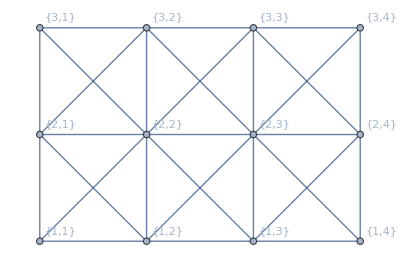

```mathematica
GraphProduct[PathGraph[Range[3]],PathGraph[Range[4]],"Normal",VertexLabels->"Name",GraphLayout->"GridEmbedding"]
```

#### Tensor Product

The tensor product of graphs has an edge between two pairs of vertices if both coordinates are adjacent.

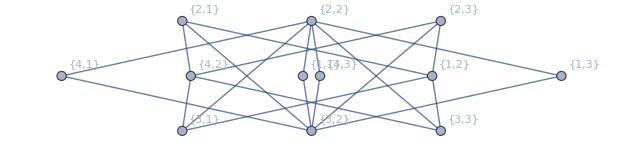

```mathematica
GraphProduct[G,PathGraph[Range[3]],"Tensor",VertexLabels->"Name"]
```

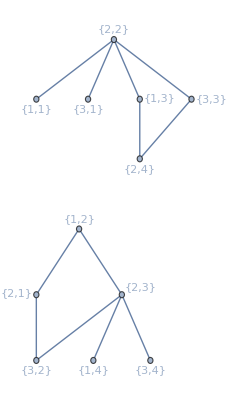

```mathematica
GraphProduct[PathGraph[Range[3]],PathGraph[Range[4]],"Tensor",VertexLabels->"Name",GraphLayout->"LayeredEmbedding"]
```

## Structures in Graphs

We want to study the structure of graphs. Do they contain long cycles? We need a vocabulary to discuss this.

### Subgraphs

Let  be a graph. A subgraph  is a graph such that   and .

The graph 1-3-2-4 is a subgraph of our example graph.

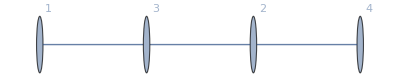

```mathematica
Graph[{2<->3,2<->4,3<->1},VertexLabels->"Name"]
```

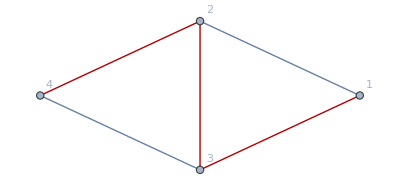

```mathematica
HighlightGraph[G,{2<->3,2<->4,3<->1}]
```

### Induced Subgraphs

Let  be a graph. An induced subgraph  is a graph such that   and  consists of those edges of  whose endpoints are both in . Note that every induced subgraph is also a subgraph. The Mathematica command ‘subgraph’ actually refers to an induced subgraph.

```mathematica
Subgraph[G,{2,3,4}]
```

-Graphics-

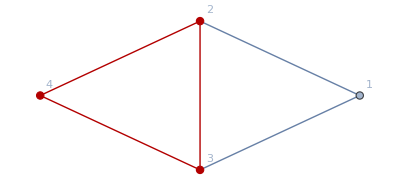

```mathematica
HighlightGraph[G,Subgraph[G,{2,3,4}]]
```

### Minors: Contracting edges

A minor is a generalization of a subgraph. An induced subgraph comes from deleting vertices. A subgraph comes from deleting vertices or edges. A minor of a graph G results from repeatedly deleting vertices or edges, and contracting by edges from G.

To contract by an edge, we identify the two vertices that are incident to that edge. We treat them as a single vertex whose neighbors are the union of the neighbors of the two vertices that it replaces.

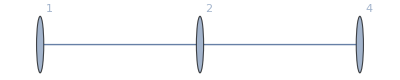

```mathematica
EdgeContract[G,2<->3]
```

To see the significance of the concept of minor, consider a graph H:

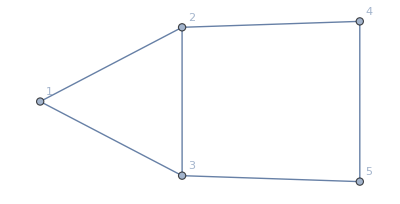

```mathematica
H=Graph[{1<->2,2<->3,1<->3,3<->5,2<->4,5<->4},VertexLabels->"Name"]
```

The structure of our graph G appears in H, but not as a subgraph. It appears as a minor if we contract the edge {4,5}.
Robinson-Seymour Theory seeks to understand graph structures in terms of a graph’s minors. For example, it is known that a graph can be drawn without edges crossing iff the graph does not contain  or  as a minor.

## Functions on Graphs

Let  and  be graphs. A graph homomorphism from  to  is a function  such that if , then . Note that if , we do not require that .

The language of functions can be used to describe the subgraphs and minors that appear in a graph. For example, if  is a graph homomorphism and f is injective, then  is a subgraph of .  Contracting an edge is a graph homomorphism.
If  is a graph homomorphism and   is a bijection, then  exists, but it may not be a graph homomorphism. If it is a  graph homomorphism, then we say that  is an isomorphism of graphs. The function preserves the structure of the graph, and just changes the names of the vertices.

Now we draw an example of a homomorphism . This particular homomorphism is not injective.

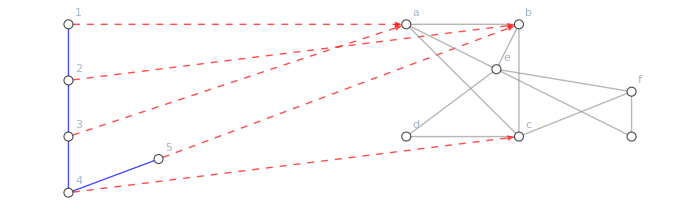
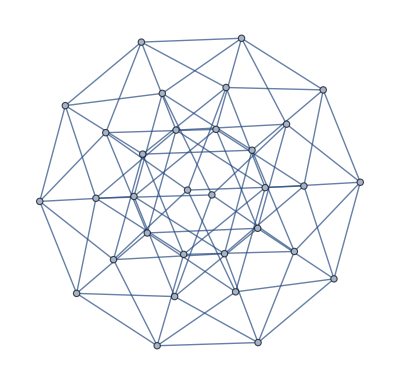

```mathematica
(*---Source graph (5 vertices)---*)edgesG={1<->2,2<->3,3<->4,4<->5}; (*path on 5 vertices*)
gHomEx=Graph[edgesG,VertexLabels->"Name",PlotLabel->"gHomEx"];

(*---Target graph (7 vertices)---*)
(*choose a fairly connected target so nonedges of G can map to edges of H*)
edgesH={a<->b,b<->c,a<->c,(*triangle among a,b,c*)c<->d,d<->e,e<->f,f<->g,g<->a,(*extra connections around*)b<->e,c<->f              (*some cross links*)};
hHomEx=Graph[edgesH,VertexLabels->"Name",PlotLabel->"hHomEx"];

(*---A homomorphism f:gHomEx->hHomEx---*)
(*Non-injective:vertices 1 and 3 both map to'a';2 and 5 both map to'b'*)
mapping={1->a,2->b,3->a,4->c,5->b};

(*---Visualize:place G on the left,H on the right,and draw red arrows for the vertex map---*)
coordsG={{0,0},{0,-0.5},{0,-1},{0,-1.5},{0.8,-1.2}}; (*some irregular column for visual interest*)

coordsH={{3,0},{4,0},{4,-1},{3,-1},{3.8,-0.4},{5,-0.6},{5,-1}}; (*positions for a,b,c,d,e,f,g respectively*)

vertexList=Join[{1,2,3,4,5},{a,b,c,d,e,f,g}];
vertexCoords=Join[coordsG,coordsH];

mapEdges=DirectedEdge@@@mapping; (*arrows from source vertices to images*)

homGraph=Graph[Join[edgesG,edgesH,mapEdges],VertexLabels->"Name",VertexCoordinates->vertexCoords,VertexSize->Medium,EdgeStyle->(Join[Thread[edgesG->Directive[Thick,Blue]],(*source edges:thick blue*)Thread[edgesH->GrayLevel[0.6]],(*target edges:light gray*)Thread[mapEdges->Directive[Red,Thick,Dashed,Arrowheads[0.02]]]  (*mapping arrows*)]),VertexStyle->(Thread[vertexList->White]),ImageSize->700];

homGraph
```

## Trees

A tree is a connected graph that does not have any subgraphs that are isomorphic to cycles of  vertices or more.

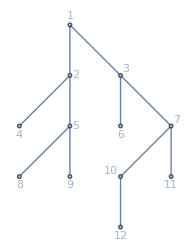

```mathematica
edges={1<->2,1<->3,2<->4,2<->5,3<->6,3<->7,5<->8,5<->9,7<->10,7<->11,10<->12};(*Define edges of a tree*)
(*Draw the tree with a layered layout*)
treeGraph=Graph[edges,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

Trees are sometimes considered to have a special vertex, called a root. 

Some properties of Trees:
-The number of edges is one less than the number of vertices.
-There is a unique path between any two vertices.
-If there are more than 2 vertices, there is always at least one leaf, a vertex with degree 1.
-Every tree is bipartite (a subgraph of a complete bipartite graph).
-Trees have a recursive structure. The root can be thought of having two “subtrees” as children.

Terminology related to trees:
- Each vertex  (except the root) has a unique neighbor that is on the path to the root. This vertex is called ’s parent.
- The neighbors of a vertex that are not on the path to the root are called ’s children.
- A vertex’s ancestors are the vertex’s parent, and that parent’s parent, and so forth, including the root.
- A vertex’s descendants are the vertex’s children, their children, and so forth, including the leaves.
- The depth of a vertex is the length of the path to the root. The depth of a tree is the largest depth of a vertex.
- The height of a vertex is the length of the longest path to a leaf, excluding the paths that pass through an ancestor of the vertex.

### Binary Trees

The nicest trees have a regular structure. A binary tree is a tree where each vertex has degree , except for the root and the leaves. A binary tree is balanced if all vertices are as close to the root as possible.

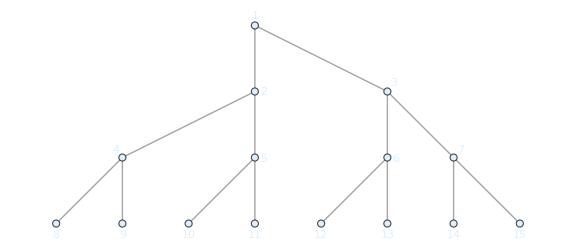

```mathematica
(*Define the edges for a balanced binary tree of depth 4*)edges=Flatten[Table[{i<->2 i,i<->2 i+1},{i,1,7}  (*internal nodes 1..7,each gets 2 children*)]];

(*Draw the tree and assign it to balancedBinaryTree*)
balancedBinaryTree=TreeGraph[edges,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding",VertexStyle->LightBlue,EdgeStyle->Gray,ImageSize->Large];

balancedBinaryTree
```